```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["4_cv.dat","Table"];
MagnetData = Import["4_magnetization.dat","Table"];
SusceptData = Import["4_susceptibility.dat","Table"];
```

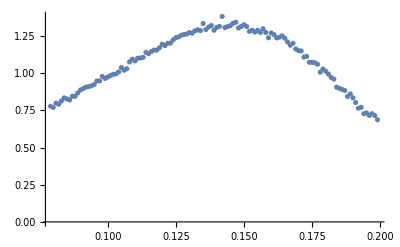

```mathematica
ListPlot[Take[SusceptData,{80,200}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{80,200}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,1.4},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{1.31062 ⅇ^(-170.629 (-0.140144+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.31062 | 0.00520808 | 251.651 | 5.81602×10^-163
Sigma | 0.0541325 | 0.000495051 | 109.347 | 1.89305×10^-120
mu | 0.140144 | 0.00029008 | 483.121 | 2.36938×10^-196}

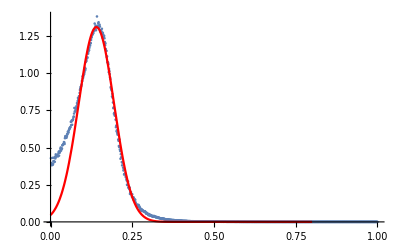

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

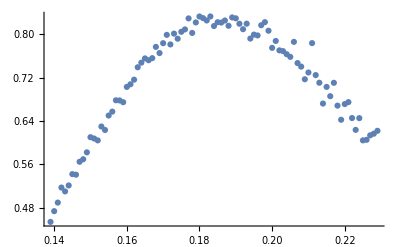

```mathematica
ListPlot[Take[CvData,{140,230}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{140,230}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{A,Sigma,mu},x]
```

FittedModel[0.826835 ⅇ^(-222.132 (-«20»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{0.826835 ⅇ^(-222.132 (-0.188156+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.826835 | 0.00285411 | 289.699 | 6.52412×10^-133
Sigma | 0.0474438 | 0.00048202 | 98.4272 | 8.33127×10^-92
mu | 0.188156 | 0.00025066 | 750.643 | 2.78346×10^-169}

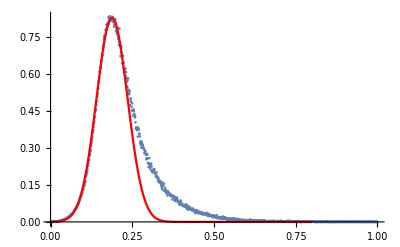

```mathematica
Show[ListPlot[CvData],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```